#### Polytropic interpolation for G2 EoS

```mathematica
latdat=Import["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/G2_stars/EoS/data/EoS_G2_prime"]
```

{{0.,1.67298×10^-6,1.67298×10^-6},{0.,0.0000312307,0.0000312307},{0.0368098,8.78773×10^-6,8.78773×10^-6},{0.0736196,-7.20746×10^-6,-7.20746×10^-6},{0.110429,0.000038993,0.000038993},{0.147239,1.64323×10^-7,1.64323×10^-7},{0.184049,0.0000564298,0.0000564298},{0.220859,0.00013196,0.00013196},{0.257669,0.000141566,0.0000259196},{0.294479,0.000190949,0.000190949},{0.331288,0.00015508,0.00015508},{0.368098,0.000301304,0.000301304},{0.404908,0.000292064,0.000292064},{0.441718,0.00033533,0.00033533},{0.478528,0.000356087,0.000356087},{0.515337,0.000470092,0.000470092},{0.552147,0.000747099,0.000747099},{0.588957,0.000821352,0.000821352},{0.625767,0.000971272,0.000971272},{0.662577,0.000921666,0.000921666},{0.699387,0.00142987,0.0000885475},{0.736196,0.00185749,0.00185749},{0.773006,0.0019786,0.0000408614},{0.809816,0.00211767,0.00211767},{0.846626,0.0021546,0.0000397255},{0.883436,0.0022343,0.0022343},{0.920245,0.00245097,0.0000758474},{0.957055,0.00254334,0.00254334},{0.993865,0.00296142,0.0000708534},{1.03068,0.00346021,0.00346021},{1.06749,0.00389707,0.0000748133},{1.10429,0.00451893,0.00451893},{1.1411,0.0050182,0.00013126},{1.17791,0.00613572,0.0000188598},{1.25153,0.0070371,0.0000263293},{1.32515,0.0101906,0.0000549543},{1.39877,0.0119938,0.000648161},{3.68098,1.07757,0.}}

```mathematica
Length[latdat]
nsat = latdat[[38,2]];
μsat = latdat[[38,1]];
μgt1=latdat[[30;;37]];
```

38

```mathematica
μPP[n_, c_, Γ_, K_]:=c+Γ*K*n^(Γ-1)/(Γ-1)
PPP[n_, Γ_, K_]:=K*n^Γ
epsPP[n_,c_,Γ_,K_]:=c*n+K*n^Γ/(Γ-1)
csPP[n_,c_,Γ_,K_]:=(Γ*PPP[n, Γ, K])/(PPP[n, Γ, K]+epsPP[n,c, Γ, K])
```

```mathematica
nFD[μ_, a_,b_]:=nsat/(Exp[a-b*μ]+1)
μFD[n_,a_,b_]:=(a-Log[nsat/n-1])/b
```

```mathematica
n1=latdat[[35,2]];
n2=latdat[[37,2]];
μ1=latdat[[35,1]];
μ2=latdat[[37,1]];
a=(μ1 Log[(n1 (n2-nsat))/(n2 (n1-nsat))])/(μ1-μ2)+Log[-1+nsat/n1];
b=Log[(n1 (n2-nsat))/(n2 (n1-nsat))]/(μ1-μ2);
μarrFD = Table[x,{x,1.5,3.5,0.5}]
narrFD = Table[nFD[μarrFD[[i]],a,b],{i,Length[μarrFD]}]
```

{1.5,2.,2.5,3.,3.5}

{0.0172736,0.0990216,0.415895,0.857843,1.03489}

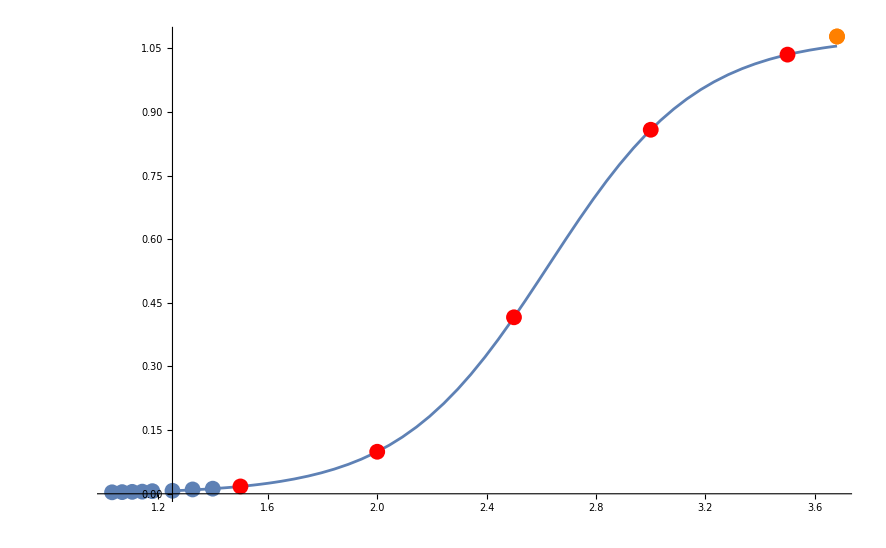

```mathematica
Plotlist={};
AppendTo[Plotlist,Plot[nFD[μ,a,b],{μ,μ1,μsat}]];
AppendTo[Plotlist,ListPlot[Transpose@{μgt1[[All,1]],μgt1[[All,2]]}]];
AppendTo[Plotlist,ListPlot[{{μsat,nsat}},PlotStyle->Orange]];
AppendTo[Plotlist,ListPlot[Transpose@{μarrFD,narrFD},PlotStyle->Red]];
Show[Plotlist, PlotRange->All]
```

```mathematica
(**nextΓ[μ0_,μ1_,K0_,n0_,n1_,Γ0_]:=NSolve[0==(Γ K0 n0^(-Γ+Γ0) (-n0^(-1+Γ)+n1^(-1+Γ)))/(1-Γ)-μ0+μ1,Γ]**)
nextΓ[μ0_,μ1_,K0_,n0_,n1_,Γ0_]:=Γ/.FindRoot[(Γ K0 n0^(-Γ+Γ0) (-n0^(-1+Γ)+n1^(-1+Γ)))/(1-Γ)-μ0+μ1,{Γ,1.5},PrecisionGoal->6]
nextK[n0_,Γ1_,P0_]:=n0^-Γ1 P0
nextc[μ1_,n1_,K1_,Γ1_]:=μ1-(K1 n1^(-1+Γ1) Γ1)/(Γ1-1)
nextP[n1_,Γ1_,K1_]:=K1 n1^Γ1
```

```mathematica
narr = Join[μgt1[[All,2]],narrFD];
μarr = Join[μgt1[[All,1]],μarrFD];
Length[narr]
```

13

```mathematica
Γ00=5/3//N;
c00=1;
Γarr = Table[0,{i,Length[narr]}];
carr = Table[0,{i,Length[narr]}];
Karr = Table[0,{i,Length[narr]}];
Parr = Table[0,{i,Length[narr]}];
Γarr[[1]]=Γ00;
carr[[1]]=c00;
Karr[[1]]=(μarr[[1]]-carr[[1]])*(Γarr[[1]]-1)*narr[[1]]^(1-Γarr[[1]])/Γarr[[1]];
Parr[[1]]=Karr[[1]]*narr[[1]]^Γarr[[1]];
```

```mathematica
For[i=2,i<Length[narr]+1,i++,
Γarr[[i]]=nextΓ[μarr[[i-1]],μarr[[i]],Karr[[i-1]],narr[[i-1]],narr[[i]],Γarr[[i-1]]];
Karr[[i]]=nextK[narr[[i-1]],Γarr[[i]],Parr[[i-1]]];
carr[[i]]=nextc[μarr[[i]],narr[[i]],Karr[[i]],Γarr[[i]]];
Parr[[i]]=nextP[narr[[i]],Γarr[[i]],Karr[[i]]];
]
```

```mathematica
μarr;
narr;
Parr;
carr
Karr
Γarr
Parr
Export["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/TOV_new/cKgP_DM.csv",Table[{carr[[i]],Karr[[i]],Γarr[[i]],Parr[[i]]},{i,1,Length[Parr]}], "CSV"]
```

{1,1.0173,1.00712,1.00568,0.889334,1.0193,-0.184191,1.00369,0.125906,-1.12189,-0.591396,1.61393,2.28278}

{0.536344,2.88518×10^25,2.57787×10^6,928795.,3.70119,166024.,0.333626,59.6124,0.558216,0.357475,0.376984,0.582041,0.815693}

{1.66667,12.1225,4.21596,4.0269,1.6787,3.78157,1.13505,2.26572,1.20977,1.09996,1.12294,1.61801,3.81907}

{0.0000424568,0.000179435,0.00033495,0.000510806,0.000715873,0.00120211,0.00183007,0.00264716,0.00411567,0.0280925,0.140755,0.454158,0.929846}

/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/TOV new/cKgP_DM.csv

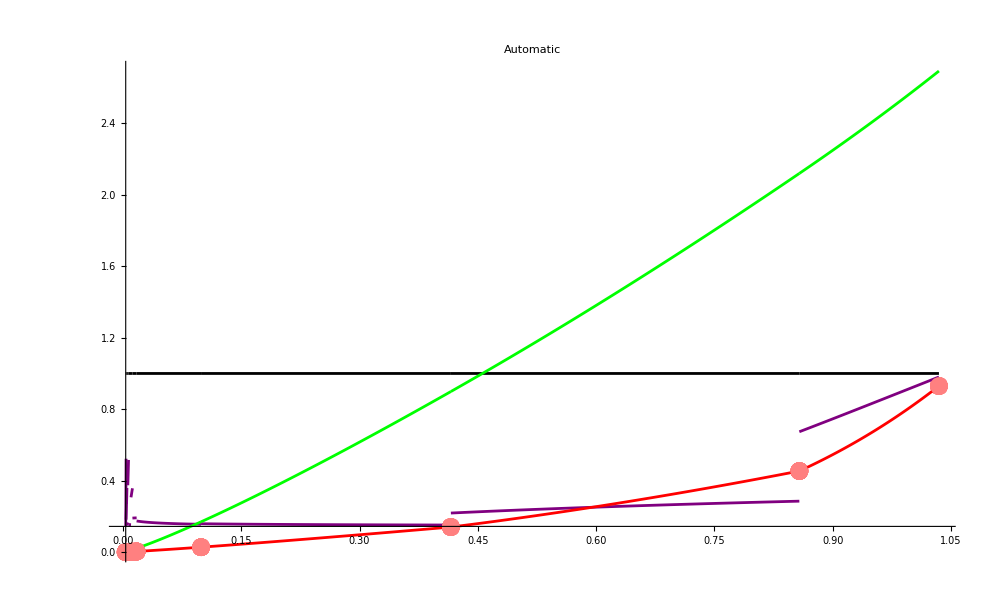

```mathematica
Plotlist={};
For[i=2,i<Length[narr]+1,i++,
(**AppendTo[Plotlist,Plot[μPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Blue]];
AppendTo[Plotlist,ListPlot[Transpose@{narr,μarr}]];**)
AppendTo[Plotlist,Plot[csPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Purple]];
AppendTo[Plotlist,Plot[1,{n,narr[[i-1]],narr[[i]]},PlotStyle->Black]];
AppendTo[Plotlist,Plot[PPP[n, Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Red]];
AppendTo[Plotlist,Plot[epsPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Green]];
AppendTo[Plotlist,ListPlot[Transpose@{narr,Parr},PlotStyle->Pink]];
]
Show[Plotlist,PlotRange->Automatic,PlotLabel->Automatic]
```

#### Polytropic interpolation for Hebeler soft EoS

```mathematica
1.5*10^(-2)*1000^4/197.3^3
```

1953.03

```mathematica
n0=0.16;(**fm^-3**)
neutronmass=939.5654205;(**MeV**)
hbarc=197.32698;(**MeV fm**)
```

```mathematica
Nucldat=Transpose[Import["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/G2_stars/EoS/data/EoS_Hebeler.csv","CSV"]];
Length[Nucldat]
```

17

```mathematica
novern0=Nucldat[[1]];
narr=novern0*n0/(neutronmass/hbarc)^3;
PNuclsoft=Nucldat[[3]]*hbarc^3/neutronmass^4;
ϵNuclsoft=Nucldat[[4]]*hbarc^3/neutronmass^4;
μarr=Table[(ϵNuclsoft[[i]]+PNuclsoft[[i]])/nNucl[[i]],{i,Length[nNucl]}];
```

```mathematica
Γ00=5/3;
c00=1;
Γarr = Table[0,{i,Length[narr]}];
carr = Table[0,{i,Length[narr]}];
Karr = Table[0,{i,Length[narr]}];
Parr = Table[0,{i,Length[narr]}];
Γarr[[1]]=Γ00;
carr[[1]]=c00;
Karr[[1]]=(μarr[[1]]-carr[[1]])*(Γarr[[1]]-1)*narr[[1]]^(1-Γarr[[1]])/Γarr[[1]];
Parr[[1]]=Karr[[1]]*narr[[1]]^Γarr[[1]];
For[i=2,i<=Length[narr],i++,
Γarr[[i]]=nextΓ[μarr[[i-1]],μarr[[i]],Karr[[i-1]],narr[[i-1]],narr[[i]],Γarr[[i-1]]];
Karr[[i]]=nextK[narr[[i-1]],Γarr[[i]],Parr[[i-1]]];
carr[[i]]=nextc[μarr[[i]],narr[[i]],Karr[[i]],Γarr[[i]]];
Parr[[i]]=nextP[narr[[i]],Γarr[[i]],Karr[[i]]];
]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

FindRoot::nlnum: The function value {-0.130849 (-1.+{}⟦1⟧)-1. {}⟦1⟧+{}⟦2⟧} is not a list of numbers with dimensions {1} at {Γ} = {1.5}.

ReplaceAll::reps: {FindRoot[(Γ (44.2835 (-1+{}⟦1⟧)) 0.000858473^(-Γ+5/3) (-0.000858473^Plus[«2»]+0.0010559^(-1+Γ)))/(1-Γ)-{}⟦1⟧+{}⟦2⟧,{Γ,1.5},PrecisionGoal→6]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.130849 (-1.+{}⟦1⟧)-1. {}⟦1⟧+{}⟦2⟧} is not a list of numbers with dimensions {1} at {Γ} = {1.5}.

ReplaceAll::reps: {FindRoot[(Γ (44.2835 (-1+{}⟦1⟧)) 0.000858473^(-Γ+5/3) (-0.000858473^Plus[«2»]+0.0010559^(-1+Γ)))/(1-Γ)-{}⟦1⟧+{}⟦2⟧,{Γ,1.5},PrecisionGoal→6]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.130849 (-1.+{}⟦1⟧)-1. {}⟦1⟧+{}⟦2⟧} is not a list of numbers with dimensions {1} at {Γ} = {1.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(Γ (44.2835 (-1+{}⟦1⟧)) 0.000858473^(-Γ+5/3) (-0.000858473^Plus[«2»]+0.0010559^(-1+Γ)))/(1-Γ)-{}⟦1⟧+{}⟦2⟧,{Γ,1.5},PrecisionGoal→6]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
Plotlist={};
For[i=2,i<Length[narr]+1,i++,
AppendTo[Plotlist,Plot[μPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Blue]];
AppendTo[Plotlist,Plot[PPP[n, Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Red]];
AppendTo[Plotlist,Plot[epsPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Green]];
AppendTo[Plotlist,ListPlot[Transpose@{narr,μarr}]];
AppendTo[Plotlist,ListPlot[Transpose@{narr,Parr}]];
]
(**Show[Plotlist,PlotRange->{{0,0.004},{0,0.0001}},PlotLabel->Automatic]**)
Show[Plotlist,PlotRange->All,PlotLabel->Automatic]
```

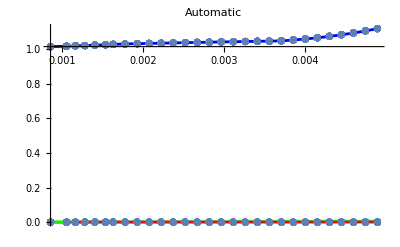

```mathematica
Parr
Table[epsPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]}]
```

#### Polytropic interpolation for Hebeler stiff EoS

```mathematica
n0=0.16;(**fm^-3**)
neutronmass=939.5654205;(**MeV**)
hbarc=197.32698;(**MeV fm**)
```

```mathematica
Nucldat=Transpose[Import["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/G2_stars/EoS/data/EoS_Hebeler.csv","CSV"]];
Length[Nucldat]
```

17

```mathematica
novern0=Nucldat[[1]];
narr=novern0*n0/(neutronmass/hbarc)^3;
PNucl=Nucldat[[13]]*hbarc^3/neutronmass^4;
ϵNucl=Nucldat[[14]]*hbarc^3/neutronmass^4;
μarr=Table[(ϵNucl[[i]]+PNucl[[i]])/nNucl[[i]],{i,Length[nNucl]}];
```

```mathematica
Γ00=5/3;
c00=1;
Γarr = Table[0,{i,Length[narr]}];
carr = Table[0,{i,Length[narr]}];
Karr = Table[0,{i,Length[narr]}];
Parr = Table[0,{i,Length[narr]}];
Γarr[[1]]=Γ00;
carr[[1]]=c00;
Karr[[1]]=(μarr[[1]]-carr[[1]])*(Γarr[[1]]-1)*narr[[1]]^(1-Γarr[[1]])/Γarr[[1]];
Parr[[1]]=Karr[[1]]*narr[[1]]^Γarr[[1]];
For[i=2,i<=Length[narr],i++,
Γarr[[i]]=nextΓ[μarr[[i-1]],μarr[[i]],Karr[[i-1]],narr[[i-1]],narr[[i]],Γarr[[i-1]]];
Karr[[i]]=nextK[narr[[i-1]],Γarr[[i]],Parr[[i-1]]];
carr[[i]]=nextc[μarr[[i]],narr[[i]],Karr[[i]],Γarr[[i]]];
Parr[[i]]=nextP[narr[[i]],Γarr[[i]],Karr[[i]]];
]
```

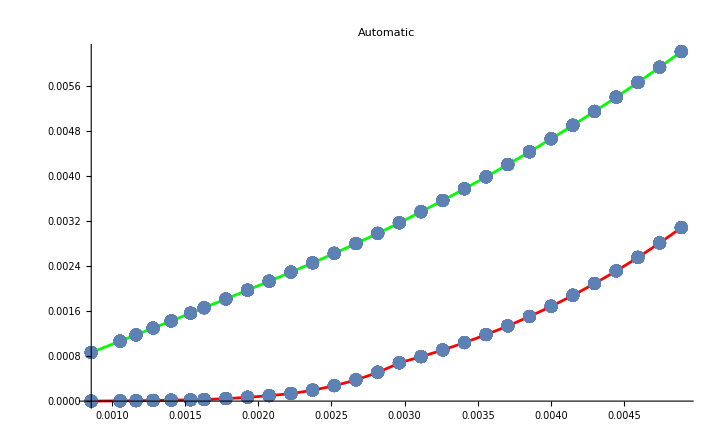

```mathematica
Plotlist={};
For[i=2,i<Length[narr]+1,i++,
(**AppendTo[Plotlist,Plot[μPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Blue]];**)
AppendTo[Plotlist,Plot[PPP[n, Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Red]];
AppendTo[Plotlist,Plot[epsPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Green]];
(**AppendTo[Plotlist,ListPlot[Transpose@{narr,μarr}]];**)
AppendTo[Plotlist,ListPlot[Transpose@{narr,PNucl}]];
AppendTo[Plotlist,ListPlot[Transpose@{narr,ϵNucl}]];
]
(**Show[Plotlist,PlotRange->{{0,0.004},{0,0.0001}},PlotLabel->Automatic]**)
Show[Plotlist,PlotRange->All,PlotLabel->Automatic]
```

#### Polytropic interpolation for Hebeler soft plus 1

```mathematica
n0=0.16;(**fm^-3**)
neutronmass=939.5654205;(**MeV**)
hbarc=197.32698;(**MeV fm**)
```

```mathematica
Nucldat=Transpose[Import["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/G2_stars/EoS/data/EoS_Hebeler.csv","CSV"]];
Length[Nucldat]
EoSI=Transpose[Import["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/G2_stars/EoS/data/EoS_I.csv","CSV"]];
nEoSI=EoSI[[1]]*n0/(neutronmass/hbarc)^3;
PEoSI=EoSI[[2]]*hbarc^3/neutronmass^4;
ϵEoSI=EoSI[[3]]*hbarc^3/neutronmass^4;
μEoSI=EoSI[[4]]/(neutronmass/1000);
```

17

```mathematica
novern0=Nucldat[[1]][[;;6]];
narr=novern0*n0/(neutronmass/hbarc)^3;
PNucl=Nucldat[[3]][[;;6]]*hbarc^3/neutronmass^4;
ϵNucl=Nucldat[[4]][[;;6]]*hbarc^3/neutronmass^4;
μarr=Table[(ϵNucl[[i]]+PNucl[[i]])/narr[[i]],{i,Length[narr]}];
(** EoS I **)
AppendTo[narr,1.1*n0/(neutronmass/hbarc)^3];
AppendTo[narr,5.9*n0/(neutronmass/hbarc)^3];
AppendTo[narr,7.5*n0/(neutronmass/hbarc)^3];
AppendTo[μarr,0.9657/(neutronmass/1000)];
AppendTo[μarr,1.653/(neutronmass/1000)];
AppendTo[μarr,1.772/(neutronmass/1000)];
```

```mathematica
Γ00=5/3//N;
c00=1;
Γarr = Table[0,{i,Length[narr]}];
carr = Table[0,{i,Length[narr]}];
Karr = Table[0,{i,Length[narr]}];
Parr = Table[0,{i,Length[narr]}];
Γarr[[1]]=Γ00;
carr[[1]]=c00;
Karr[[1]]=(μarr[[1]]-carr[[1]])*(Γarr[[1]]-1)*narr[[1]]^(1-Γarr[[1]])/Γarr[[1]];
Parr[[1]]=Karr[[1]]*narr[[1]]^Γarr[[1]];
For[i=2,i<=Length[narr],i++,
Γarr[[i]]=nextΓ[μarr[[i-1]],μarr[[i]],Karr[[i-1]],narr[[i-1]],narr[[i]],Γarr[[i-1]]];
Karr[[i]]=nextK[narr[[i-1]],Γarr[[i]],Parr[[i-1]]];
carr[[i]]=nextc[μarr[[i]],narr[[i]],Karr[[i]],Γarr[[i]]];
Parr[[i]]=nextP[narr[[i]],Γarr[[i]],Karr[[i]]];
Print[Γarr[[i]], " ",Karr[[i]], " ",carr[[i]], " ",Parr[[i]]]
]
```

1.7853 1.49918 1.00133 7.27971×10^-6

2.59616 388.394 1.00579 9.39962×10^-6

2.09613 13.2547 1.00348 0.0000114752

2.85983 2143.89 1.00684 0.000014946

2.10359 14.9381 1.00292 0.0000180427

3.39908 65897.4 1.00866 0.0000220406

3.166 14761. 1.00806 0.00449462

1.02401 0.575916 -20.1625 0.00574651

```mathematica
μarr;
narr;
Parr;
carr
Karr
Γarr
Parr
Export["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/TOV_new/cKgP_EoSI.csv",Table[{carr[[i]],Karr[[i]],Γarr[[i]],Parr[[i]]},{i,1,Length[Parr]}], "CSV"]
```

{1,1.00133,1.00579,1.00348,1.00684,1.00292,1.00866,1.00806,-20.1625}

{0.648752,1.49918,388.394,13.2547,2143.89,14.9381,65897.4,14761.,0.575916}

{1.66667,1.7853,2.59616,2.09613,2.85983,2.10359,3.39908,3.166,1.02401}

{5.03064×10^-6,7.27971×10^-6,9.39962×10^-6,0.0000114752,0.000014946,0.0000180427,0.0000220406,0.00449462,0.00574651}

/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/TOV new/cKgP_EoSI.csv

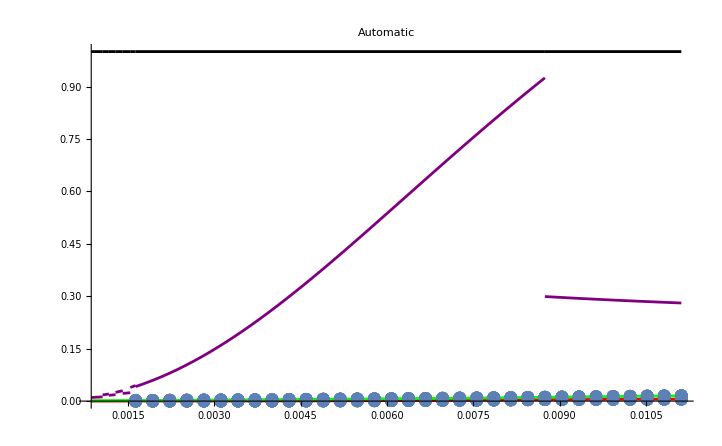

```mathematica
Plotlist={};
For[i=2,i<Length[narr]+1,i++,
(**AppendTo[Plotlist,Plot[μPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Blue]];
(**AppendTo[Plotlist,ListPlot[Transpose@{narr,μarr}]];**)
AppendTo[Plotlist,ListPlot[Transpose@{nEoSI,μEoSI}]];**)
AppendTo[Plotlist,Plot[PPP[n, Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Red]];
AppendTo[Plotlist,Plot[epsPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Green]];
AppendTo[Plotlist,Plot[1,{n,narr[[i-1]],narr[[i]]},PlotStyle->Black]];
AppendTo[Plotlist,Plot[csPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Purple]];
AppendTo[Plotlist,ListPlot[Transpose@{nEoSI,PEoSI}]];
AppendTo[Plotlist,ListPlot[Transpose@{nEoSI,ϵEoSI}]];
]
(**Show[Plotlist,PlotRange->{{0,0.004},{0,0.0001}},PlotLabel->Automatic]**)
Show[Plotlist,PlotRange->All,PlotLabel->Automatic]
```

#### Polytropic interpolation for Hebeler stiff plus 2

```mathematica
n0=0.16;(**fm^-3**)
neutronmass=939.5654205;(**MeV**)
hbarc=197.32698;(**MeV fm**)
```

```mathematica
Nucldat=Transpose[Import["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/G2_stars/EoS/data/EoS_Hebeler.csv","CSV"]];
Length[Nucldat]
EoSII=Transpose[Import["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/G2_stars/EoS/data/EoS_II.csv","CSV"]];
nEoSII=EoSII[[1]]*n0/(neutronmass/hbarc)^3;
PEoSII=EoSII[[2]]*hbarc^3/neutronmass^4;
ϵEoSII=EoSII[[3]]*hbarc^3/neutronmass^4;
μEoSII=EoSII[[4]]/(neutronmass/1000);
```

17

```mathematica
novern0=Nucldat[[1]][[;;6]];
narr=novern0*n0/(neutronmass/hbarc)^3;
PNucl=Nucldat[[13]][[;;6]]*hbarc^3/neutronmass^4;
ϵNucl=Nucldat[[14]][[;;6]]*hbarc^3/neutronmass^4;
μarr=Table[(ϵNucl[[i]]+PNucl[[i]])/narr[[i]],{i,Length[narr]}];
(** EoS II **)
AppendTo[narr,1.1*n0/(neutronmass/hbarc)^3];
AppendTo[narr,2.7*n0/(neutronmass/hbarc)^3];
AppendTo[narr,4.5*n0/(neutronmass/hbarc)^3];
AppendTo[μarr,0.9775/(neutronmass/1000)];
AppendTo[μarr,1.351/(neutronmass/1000)];
AppendTo[μarr,1.544/(neutronmass/1000)];
```

```mathematica
Γ00=5/3;
c00=1;
Γarr = Table[0,{i,Length[narr]}];
carr = Table[0,{i,Length[narr]}];
Karr = Table[0,{i,Length[narr]}];
Parr = Table[0,{i,Length[narr]}];
Γarr[[1]]=Γ00;
carr[[1]]=c00;
Karr[[1]]=(μarr[[1]]-carr[[1]])*(Γarr[[1]]-1)*narr[[1]]^(1-Γarr[[1]])/Γarr[[1]];
Parr[[1]]=Karr[[1]]*narr[[1]]^Γarr[[1]];
For[i=2,i<=Length[narr],i++,
Γarr[[i]]=nextΓ[μarr[[i-1]],μarr[[i]],Karr[[i-1]],narr[[i-1]],narr[[i]],Γarr[[i-1]]];
Karr[[i]]=nextK[narr[[i-1]],Γarr[[i]],Parr[[i-1]]];
carr[[i]]=nextc[μarr[[i]],narr[[i]],Karr[[i]],Γarr[[i]]];
Parr[[i]]=nextP[narr[[i]],Γarr[[i]],Karr[[i]]];
]
For[i=1,i<=Length[narr],i++,Print[Γarr[[i]], " ",Karr[[i]], " ",carr[[i]], " ",Parr[[i]]]]
```

5/3 0.821164 1 6.36758×10^-6

2.44522 200.304 1.00599 0.000010563

2.32993 90.8951 1.00539 0.0000132862

3.2246 38295.8 1.00884 0.0000180592

2.33372 101.507 1.00461 0.0000224054

3.07867 13527.3 1.00889 0.0000295145

2.5692 498.788 1.00589 0.0000343348

4.03004 5.89281×10^6 1.01237 0.00128037

1.19522 0.940091 -0.520893 0.00235773

```mathematica
μarr;
narr;
Parr;
carr
Karr
Γarr
Parr
Export["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/TOV_new/cKgP_EoSII.csv",Table[{carr[[i]],Karr[[i]],Γarr[[i]],Parr[[i]]},{i,1,Length[Parr]}], "CSV"]
```

{1,1.00599,1.00539,1.00884,1.00461,1.00889,1.00589,1.01237,-0.520893}

{0.821164,200.304,90.8951,38295.8,101.507,13527.3,498.788,5.89281×10^6,0.940091}

{5/3,2.44522,2.32993,3.2246,2.33372,3.07867,2.5692,4.03004,1.19522}

{6.36758×10^-6,0.000010563,0.0000132862,0.0000180592,0.0000224054,0.0000295145,0.0000343348,0.00128037,0.00235773}

/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/TOV new/cKgP_EoSII.csv

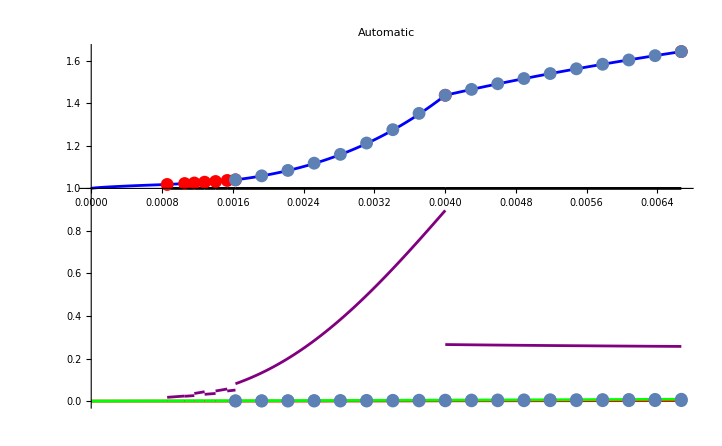

```mathematica
Plotlist={};
AppendTo[Plotlist,Plot[μPP[n, carr[[1]], Γarr[[1]], Karr[[1]]],{n,0,narr[[1]]},PlotStyle->Blue]];
AppendTo[Plotlist,Plot[PPP[n, Γarr[[1]], Karr[[1]]],{n,0,narr[[1]]},PlotStyle->Red]];
AppendTo[Plotlist,Plot[epsPP[n, carr[[1]], Γarr[[1]], Karr[[1]]],{n,0,narr[[1]]},PlotStyle->Green]];
For[i=2,i<Length[narr]+1,i++,
AppendTo[Plotlist,Plot[μPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Blue]];
AppendTo[Plotlist,Plot[PPP[n, Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Red]];
AppendTo[Plotlist,Plot[epsPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Green]];
AppendTo[Plotlist,Plot[1,{n,narr[[i-1]],narr[[i]]},PlotStyle->Black]];
AppendTo[Plotlist,Plot[csPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Purple]];
]
AppendTo[Plotlist,ListPlot[Transpose@{narr,μarr},PlotStyle->Red]];
AppendTo[Plotlist,ListPlot[Transpose@{nEoSII,μEoSII}]];
AppendTo[Plotlist,ListPlot[Transpose@{nEoSII,PEoSII}]];
AppendTo[Plotlist,ListPlot[Transpose@{nEoSII,ϵEoSII}]];
(**Show[Plotlist,PlotRange->{{0,0.01},{0,0.001}},PlotLabel->Automatic]**)
Show[Plotlist,PlotRange->All,PlotLabel->Automatic]
```

```mathematica
4*Pi*n r^2/Sqrt[1-2m/r]
Integrate[4*Pi*n r^2/Sqrt[1-2m/r],{r,0,r0}]
Integrate[4*Pi*r^2*ϵ,{r,0,r0}]
```

(4 n π r^2)/(√(1-(2 m)/r))

ConditionalExpression[(2 n π (r0 √(2-r0/m) (15 m^2+5 m r0+2 r0^2)-30 m^(5/2) √r0 ArcCsc[(√2 √m)/(√r0)]))/(3 √(-r0/m)), Re[m/r0]<0||2 Re[m/r0]>1||m/r0∉ℝ]

4/3 π r0^3 ϵ